### The solution to the periodic BC problem:

```mathematica
FindSequenceFunction[{{4,3},{6,4},{8,7},{10,11},{12,18},{14,29},{16,47},{18,76},{20,123},{22,199}},n]
```

1/2 (5 Fibonacci[1/2 (-2+n)]+LucasL[1/2 (-2+n)])

```mathematica
Table[1/2 (5 Fibonacci[1/2 (-2+n)]+LucasL[1/2 (-2+n)]),{n,2,24,2}]
```

{1,3,4,7,11,18,29,47,76,123,199,322}

Extrapolation agrees ^^^

### With 1-shift and L-R parity inversion, the config number is 4x:

```mathematica
function[n_]:=2 (5 Fibonacci[1/2 (-2+n)]+LucasL[1/2 (-2+n)])
```

### Find asymptotics:

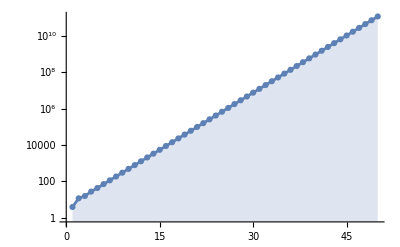

```mathematica
ListLogPlot[Table[function[n],{n,2,100,2}],Filling->Axis,Mesh->All,Joined->True]
```

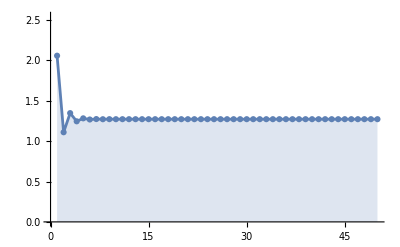

```mathematica
ListPlot[Table[function[n+1]/function[n],{n,2,100,2}],Filling->Axis,Mesh->All,Joined->True]
```

Exponent:

```mathematica
Limit[function[n+1]/function[n],n-> Infinity]
```

√(1/2 (1+√5))

```mathematica
N[√(1/2 (1+√5))]
```

1.27202

```mathematica
asymptFct[n_]:=(√(1/2 (1+√5)))^n
```

Constant retrieval:

```mathematica
Limit[function[n]/asymptFct[n],n-> Infinity]
```

4

```mathematica
constant=4;
```

### Plot comparison:

```mathematica
{data1,data2} =Transpose[Table[{constant*asymptFct[n],function[n]},{n,100}]];
```

```mathematica
ListLogPlot[{data1, data2}, Joined->True, PlotLabels->{Asymptotic, Analytic},Filling->Axis]
```

-Graphics-

### Extreme case (computed with recursive function):

```mathematica
FindSequenceFunction[{{4,3},{6,4},{8,7},{10,11},{12,18},{14,29},{16,47},{18,76},{20,123},{22,199},{24,322},{26,521},{28,843},{30,1364},{32,2207},{34,3571},{36,5778},{38,9349},{40,15127},{42,24476},{44,39603},{46,64079},{48,103682},{50,167761},{52,271443},{54,439204},{56,710647},{58,1149851},{60,1860498},{62,3010349},{64,4870847},{66,7881196},{68,12752043},{70,20633239},{72,33385282},{74,54018521},{76,87403803},{78,141422324},{80,228826127},{82,370248451},{84,599074578},{86,969323029},{88,1568397607},{90,2537720636},{92,4106118243},{94,6643838879},{96,10749957122},{98,17393796001},{100,28143753123},{102,45537549124},{104,73681302247},{106,119218851371},{108,192900153618},{110,312119004989},{112,505019158607},{114,817138163596},{116,1322157322203},{118,2139295485799},{120,3461452808002},{122,5600748293801},{124,9062201101803},{126,14662949395604}},n]
```

1/2 (5 Fibonacci[1/2 (-2+n)]+LucasL[1/2 (-2+n)])

The same function is found^^^